# Trikotnik in včrtana ter očrtana krožnica

## Uvod

V projektni nalogi so obravnavani objekti točka, daljica in trikotnik.
Za te objekte so implementirane funkcije za določanje osnovnih lastnosti
ter njihov grafični prikaz v dveh dimenzijah.
Posebna pozornost je namenjena včrtani in očrtani krožnici trikotnika.

## Objekt Točka

Točka predstavlja osnovni geometrijski objekt v ravnini. Določena je z dvema koordinatama (x, y), ki določata njen položaj v koordinatnem sistemu.

### Definicija objekta

Točka je v projektu predstavljena z objektom Tocka[x, y], kjer x in y sta koordinati točke v ravnini.

```mathematica
ClearAll[Tocka,Koordinate]
Koordinate[Tocka[x_,y_]]:={x,y}
```

### Primer

V nadaljevanju so definirane tri točke, ki bodo kasneje uporabljene za konstrukcijo daljic in trikotnika.

```mathematica
A1=Tocka[1,2];
B1=Tocka[5,1];
C1=Tocka[3,4];

Koordinate/@{A1,B1,C1}
```

{{1,2},{5,1},{3,4}}

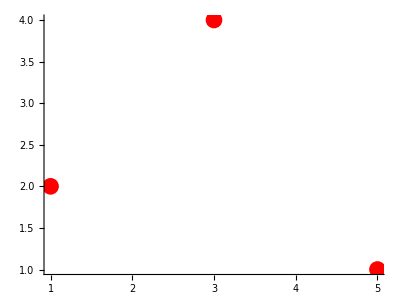

```mathematica
Graphics[{Red,PointSize[0.03],Point[Koordinate/@{A1,B1,C1}]},Axes->True]
```

## Objekt Daljica

### Definicija objekta

Daljica je določena z dvema krajiščema. V projektu je predstavljena z objektom Daljica[p1, p2], kjer sta p1 in p2 objekta tipa Točka.

```mathematica
ClearAll[Daljica,Krajišči]
Krajišči[Daljica[p1_,p2_]]:={p1,p2}
```

### Dolžina daljice

Dolžina daljice je razdalja med njenima krajiščema. Izračunana je z uporabo Evklidske razdalje med koordinatama točk.

```mathematica
Dolzina[Daljica[p1_,p2_]]:=EuclideanDistance[Koordinate[p1],Koordinate[p2]]
```

### Primer

V nadaljevanju je definirana daljica med točkama A1 in B1.

```mathematica
d1=Daljica[A1,B1];

Dolzina[d1]
```

√17

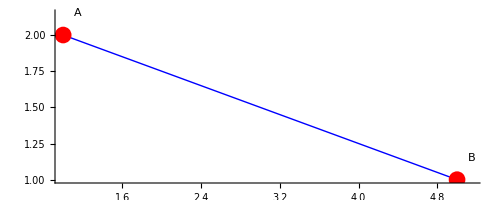

```mathematica
Graphics[{Blue,Thick,Line[Koordinate/@Krajišči[d1]],Red,PointSize[0.03],Point[Koordinate/@Krajišči[d1]],Black,Text["A",Koordinate[A1]+{0.15,0.15}],Text["B",Koordinate[B1]+{0.15,0.15}]},Axes->True]
```

## Objekt Trikotnik

### Definicija objekta

Trikotnik je določen s tremi oglišči. V projektu je predstavljen z objektom Trikotnik[p1, p2, p3], kjer so p1, p2 in p3 objekti tipa Točka.

```mathematica
ClearAll[Trikotnik,Oglisca]

Oglisca[Trikotnik[p1_,p2_,p3_]]:={p1,p2,p3}
```

### Primer

V nadaljevanju je definiran trikotnik z oglišči A1, B1 in C1.

```mathematica
t1=Trikotnik[A1,B1,C1];

Oglisca[t1]
```

{Tocka[1,2],Tocka[5,1],Tocka[3,4]}

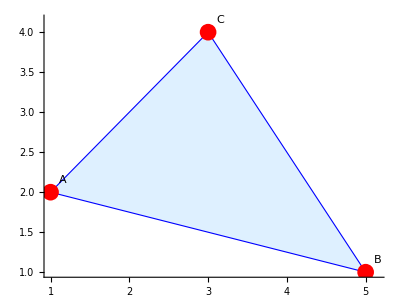

```mathematica
Graphics[{LightBlue,EdgeForm[{Blue,Thick}],Polygon[Koordinate/@Oglisca[t1]],Red,PointSize[0.03],Point[Koordinate/@Oglisca[t1]],Black,Text["A",Koordinate[A1]+{0.15,0.15}],Text["B",Koordinate[B1]+{0.15,0.15}],Text["C",Koordinate[C1]+{0.15,0.15}]},Axes->True]
```

## Lastnosti trikotnika

### Dolžine stranic

Dolžine stranic trikotnika dobimo tako, da iz njegovih oglišč sestavimo tri daljice in za vsako izračunamo dolžino.

```mathematica
ClearAll[Stranice,DolzineStranic]

Stranice[Trikotnik[p1_,p2_,p3_]]:={Daljica[p1,p2],Daljica[p2,p3],Daljica[p3,p1]}

DolzineStranic[t_]:=Dolzina/@Stranice[t]
```

```mathematica
DolzineStranic[t1]
```

{√17,√13,2 √2}

```mathematica
Association[{"AB","BC","CA"}->DolzineStranic[t1]]
```

<|{AB,BC,CA}→{√17,√13,2 √2}|>

### Obseg in ploščina

Obseg trikotnika je vsota dolžin vseh njegovih stranic. Ploščino trikotnika izračunamo s Heronovo formulo, kjer najprej določimo polovični obseg.

```mathematica
ClearAll[Obseg,Ploscina]

Obseg[t_]:=Apply[Plus,DolzineStranic[t]]

Ploscina[t_]:=Module[{a,b,c,s},{a,b,c}=DolzineStranic[t];
s=Obseg[t]/2;
Sqrt[s (s-a) (s-b) (s-c)]]
```

#### Primer

```mathematica
Association[{"Obseg"->N[Obseg[t1]],"Ploščina"->N[Ploscina[t1]]}]
```

<|Obseg→10.5571,Ploščina→5.|>

### Tip trikotnika

Tip trikotnika določimo na podlagi dolžin njegovih stranic. Trikotnik je lahko enakostranični, enakokraki ali raznostranični.

```mathematica
ClearAll[TipTrikotnika]

TipTrikotnika[t_]:=Module[{stranice},stranice=DeleteDuplicates[DolzineStranic[t]];
Which[Length[stranice]==1,"Enakostranični",Length[stranice]==2,"Enakokraki",True,"Raznostranični"]]
```

#### Primer

Določimo tip prej definiranega trikotnika.

```mathematica
TipTrikotnika[t1]
```

Raznostranični

## Včrtana krožnica

### Središče včrtane krožnice

Včrtana krožnica je krožnica, ki se dotika vseh treh stranic trikotnika.
Njeno središče leži v presečišču simetral notranjih kotov trikotnika, polmer pa je enak razdalji od središča do poljubne stranice.

```mathematica
ClearAll[SredisceVcrtane]

SredisceVcrtane[t_]:=Module[{oglišča,A,B,C,a,b,c},oglišča=Oglisca[t];
{A,B,C}=Koordinate/@oglišča;
{a,b,c}=DolzineStranic[t][[{2,3,1}]];
(a A+b B+c C)/(a+b+c)]
```

#### Primer

Določimo središče včrtane krožnice za prej definirani trikotnik .

```mathematica
N[SredisceVcrtane[t1]]
```

{2.85278,2.51319}

### Polmer včrtane krožnice

Polmer včrtane krožnice je razdalja od njenega središča do poljubne stranice trikotnika.
Izračunamo ga kot količnik med ploščino trikotnika in polovico njegovega obsega.

```mathematica
ClearAll[PolmerVcrtane]

PolmerVcrtane[t_]:=Ploscina[t]/(Obseg[t]/2)
```

#### Primer

Izračunamo polmer včrtane krožnice.

```mathematica
N[PolmerVcrtane[t1]]
```

0.947231

#### Primer prikaza včrtane krožnice

Na sliki je prikazan trikotnik skupaj z včrtano krožnico. Središče krožnice je označeno z modro točko.

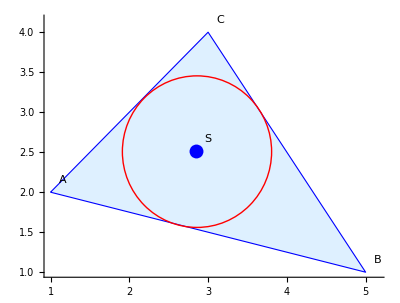

```mathematica
Graphics[{LightBlue,EdgeForm[{Blue,Thick}],Polygon[Koordinate/@Oglisca[t1]],Red,Thick,Circle[SredisceVcrtane[t1],PolmerVcrtane[t1]],Blue,PointSize[0.025],Point[SredisceVcrtane[t1]],Black,Text["A",Koordinate[A1]+{0.15,0.15}],Text["B",Koordinate[B1]+{0.15,0.15}],Text["C",Koordinate[C1]+{0.15,0.15}],Text["S",SredisceVcrtane[t1]+{0.15,0.15}]},Axes->True]
```

## Očrtana krožnica

### Središče očrtane krožnice

Očrtana krožnica je krožnica, ki poteka skozi vsa tri oglišča trikotnika. Njeno središče je presečišče simetral stranic trikotnika.

```mathematica
ClearAll[SredisceOcrtane]

SredisceOcrtane[t_]:=Module[{toc,x,y,s},toc=Koordinate/@Oglisca[t];
{x,y}/. Solve[EuclideanDistance[{x,y},toc[[1]]]==EuclideanDistance[{x,y},toc[[2]]]&&EuclideanDistance[{x,y},toc[[1]]]==EuclideanDistance[{x,y},toc[[3]]],{x,y}][[1]]]
```

#### Primer

Določimo središče očrtane krožnice za prej definirani trikotnik.

```mathematica
N[SredisceOcrtane[t1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{3.1,1.9}

### Polmer očrtane krožnice

Polmer očrtane krožnice je razdalja med njenim središčem in poljubnim ogliščem trikotnika.

```mathematica
ClearAll[PolmerOcrtane]

PolmerOcrtane[t_]:=EuclideanDistance[SredisceOcrtane[t],Koordinate[Oglisca[t][[1]]]]
```

#### Primer

Izračunamo polmer očrtane krožnice.

```mathematica
N[PolmerOcrtane[t1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

2.10238

### Primer prikaza očrtane krožnice

Na sliki je prikazan trikotnik skupaj z očrtano krožnico. Središče krožnice je označeno z modro točko.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

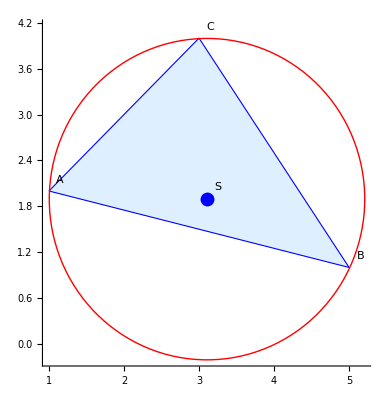

```mathematica
Graphics[{LightBlue,EdgeForm[{Blue,Thick}],Polygon[Koordinate/@Oglisca[t1]],Red,Thick,Circle[SredisceOcrtane[t1],PolmerOcrtane[t1]],Blue,PointSize[0.025],Point[SredisceOcrtane[t1]],Black,Text["A",Koordinate[A1]+{0.15,0.15}],Text["B",Koordinate[B1]+{0.15,0.15}],Text["C",Koordinate[C1]+{0.15,0.15}],Text["S",SredisceOcrtane[t1]+{0.15,0.15}]},Axes->True]
```

## Skupni prikaz krožnic

V tem delu sta na istem trikotniku prikazani včrtana in očrtana krožnica.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

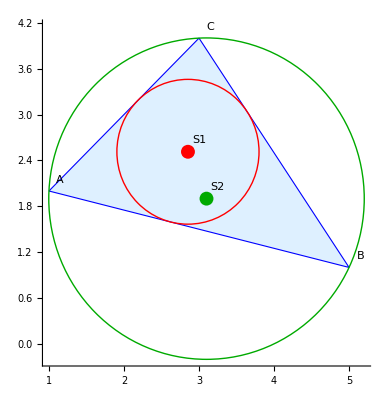

```mathematica
Graphics[{LightBlue,EdgeForm[{Blue,Thick}],Polygon[Koordinate/@Oglisca[t1]],Red,Thick,Circle[SredisceVcrtane[t1],PolmerVcrtane[t1]],Darker[Green],Thick,Circle[SredisceOcrtane[t1],PolmerOcrtane[t1]],Red,PointSize[0.025],Point[SredisceVcrtane[t1]],Darker[Green],PointSize[0.025],Point[SredisceOcrtane[t1]],Black,Text["A",Koordinate[A1]+{0.15,0.15}],Text["B",Koordinate[B1]+{0.15,0.15}],Text["C",Koordinate[C1]+{0.15,0.15}],Text["S1",SredisceVcrtane[t1]+{0.15,0.15}],Text["S2",SredisceOcrtane[t1]+{0.15,0.15}]},Axes->True]
```

## Interaktivni prikaz

V tem delu je pripravljen interaktivni prikaz trikotnika. Uporabnik lahko spreminja koordinate oglišč, program pa sproti izriše trikotnik ter njegovo včrtano in očrtano krožnico.

```mathematica
Manipulate[Module[{p1,p2,p3,t,pts,a,b,c,d,ux,uy,sO,rO,sV,rV,graf,podatki},p1=Tocka[x1,y1];
p2=Tocka[x2,y2];
p3=Tocka[x3,y3];
t=Trikotnik[p1,p2,p3];
pts=Koordinate/@Oglisca[t];
{{a,b},{c,d},{ux,uy}}=pts;
sO=Module[{xA,yA,xB,yB,xC,yC,D},{{xA,yA},{xB,yB},{xC,yC}}=pts;
D=2 (xA (yB-yC)+xB (yC-yA)+xC (yA-yB));
{((xA^2+yA^2) (yB-yC)+(xB^2+yB^2) (yC-yA)+(xC^2+yC^2) (yA-yB))/D,((xA^2+yA^2) (xC-xB)+(xB^2+yB^2) (xA-xC)+(xC^2+yC^2) (xB-xA))/D}];
rO=EuclideanDistance[sO,pts[[1]]];
sV=N[SredisceVcrtane[t]];
rV=N[PolmerVcrtane[t]];
graf=Graphics[{LightBlue,EdgeForm[{Blue,Thick}],Polygon[pts],Red,Thick,Circle[sV,rV],Darker[Green],Thick,Circle[sO,rO],Red,PointSize[0.03],Point[sV],Darker[Green],PointSize[0.03],Point[sO],Black,PointSize[0.035],Point[pts],Black,Text["A",pts[[1]]+{0.15,0.15}],Text["B",pts[[2]]+{0.15,0.15}],Text["C",pts[[3]]+{0.15,0.15}],Text["S1",sV+{0.15,0.15}],Text["S2",sO+{0.15,0.15}]},Axes->True,PlotRange->{{0,6},{0,5}},ImageSize->450];
podatki=Grid[{{"Dolžina AB",N[DolzineStranic[t][[1]]]},{"Dolžina BC",N[DolzineStranic[t][[2]]]},{"Dolžina CA",N[DolzineStranic[t][[3]]]},{"Obseg",N[Obseg[t]]},{"Ploščina",N[Ploscina[t]]},{"Tip trikotnika",TipTrikotnika[t]},{"Polmer včrtane",rV},{"Polmer očrtane",rO}},Frame->All,Spacings->{2,1}];
Column[{graf,podatki}]],{{x1,1},0,6},{{y1,2},0,5},{{x2,5},0,6},{{y2,1},0,5},{{x3,3},0,6},{{y3,4},0,5}]
```